## Input Data

```mathematica
Off[ClebschGordan::tri];
Off[ClebschGordan::phy];
Off[SixJSymbol::tri];
Off[SixJSymbol::phy];
(*ParallelEvaluate[Off[ClebschGordan::tri]];
ParallelEvaluate[Off[SixJSymbol::tri]];
ParallelEvaluate[Off[Infinity::indet]];
ParallelEvaluate[Off[ClebschGordan::phy]];
ParallelEvaluate[Off[ClebschGordan::tri]];
ParallelEvaluate[Off[NIntegrate::eincr]];
ParallelEvaluate[Off[NIntegrate::slwcon]];
ParallelEvaluate[Off[General::munfl ]];*)
SetDirectory[StringJoin[NotebookDirectory[]]]
```

C:\Users\CAMPIT\Documents\GitHub\bsmllh\nb\theDD

```mathematica
nucleus="be";
m=Piecewise[{
{{1.,4.,4.},nucleus=="be"},
{{4.,1.,1.},nucleus=="he"||nucleus=="li"}
}];
z=Piecewise[{
{{0.,2.,2.},nucleus=="be"},
{{2.,0.,0.},nucleus=="he"},
{{2.,1.,0.},nucleus=="li"}
}];
fileName=StringJoin[nucleus,"/",nucleus,"0"];
importedData=Import[FileNameJoin[{NotebookDirectory[], StringJoin[fileName,".wf"]}], "Table"];
γ={};
dataList={};
tempList={};
AppendTo[γ,importedData⟦1⟧];
Do[
If[IntegerQ@importedData⟦i,1⟧,
AppendTo[γ,importedData⟦i⟧];
AppendTo[dataList,tempList];
tempList={};
,
AppendTo[tempList,importedData⟦i⟧];
];
,{i,2,Length@importedData}];
AppendTo[dataList,tempList];
Clear[tempList];
Cij={};
αij={};
βij={};
Do[
tempCij={};
tempαij={};
tempβij={};
Do[
If[i==j,AppendTo[tempCij,dataList⟦k,i,3⟧dataList⟦k,j,3⟧]
,AppendTo[tempCij,2dataList⟦k,i,3⟧dataList⟦k,j,3⟧]];
AppendTo[tempαij,2(dataList⟦k,i,1⟧+dataList⟦k,j,1⟧)];
AppendTo[tempβij,2(dataList⟦k,i,2⟧+dataList⟦k,j,2⟧)];
,{i,1,Length@dataList⟦k,All,3⟧},{j,1,i}];
AppendTo[Cij,tempCij];
AppendTo[αij,tempαij];
AppendTo[βij,tempβij];
,{k,1,Length@γ}];
α=2.dataList⟦All,All,1⟧;
β=2.dataList⟦All,All,2⟧;
𝒞=dataList⟦All,All,3⟧;
(*
T=Module[{c,s},
c=-√((m⟦1⟧m⟦2⟧)/((m⟦1⟧+m⟦3⟧)(m⟦2⟧+m⟦3⟧)));
s=(-1)^(2-1)Sign[1-2] √(1-c^2);
{{c,s},{-s,c}}];
T={{-√((m⟦1⟧m⟦2⟧)/((m⟦1⟧+m⟦3⟧)(m⟦2⟧+m⟦3⟧))),-√((m⟦3⟧(m⟦1⟧+m⟦2⟧+m⟦3⟧))/((m⟦1⟧+m⟦3⟧)(m⟦2⟧+m⟦3⟧)))},{√((m⟦3⟧(m⟦1⟧+m⟦2⟧+m⟦3⟧))/((m⟦1⟧+m⟦3⟧)(m⟦2⟧+m⟦3⟧))),-√((m⟦1⟧m⟦2⟧)/((m⟦1⟧+m⟦3⟧)(m⟦2⟧+m⟦3⟧)))}};
T={{-m⟦1⟧/(m⟦3⟧+m⟦1⟧),-1},{(m⟦3⟧(m⟦1⟧+m⟦2⟧+m⟦3⟧))/((m⟦2⟧+m⟦3⟧)(m⟦1⟧+m⟦3⟧)),-m⟦2⟧/(m⟦2⟧+m⟦3⟧)}};
T={{-m⟦1⟧/(m⟦2⟧+m⟦1⟧),1},{-(m⟦2⟧(m⟦1⟧+m⟦2⟧+m⟦3⟧))/((m⟦2⟧+m⟦1⟧)(m⟦2⟧+m⟦3⟧)),-m⟦3⟧/(m⟦2⟧+m⟦3⟧)}};
*)
T={{-√((m⟦1⟧m⟦2⟧)/((m⟦1⟧+m⟦3⟧)(m⟦2⟧+m⟦3⟧))),-√((m⟦3⟧(m⟦1⟧+m⟦2⟧+m⟦3⟧))/((m⟦1⟧+m⟦3⟧)(m⟦2⟧+m⟦3⟧)))},{√((m⟦3⟧(m⟦1⟧+m⟦2⟧+m⟦3⟧))/((m⟦1⟧+m⟦3⟧)(m⟦2⟧+m⟦3⟧))),-√((m⟦1⟧m⟦2⟧)/((m⟦1⟧+m⟦3⟧)(m⟦2⟧+m⟦3⟧)))}};
If[nucleus=="be",T={{-m⟦1⟧/(m⟦3⟧+m⟦1⟧),-1},{(m⟦3⟧(m⟦1⟧+m⟦2⟧+m⟦3⟧))/((m⟦2⟧+m⟦3⟧)(m⟦1⟧+m⟦3⟧)),-m⟦2⟧/(m⟦2⟧+m⟦3⟧)}};];
Q=T.{{1,0},{p,1}};
Protect[p];
Det[T]
μij=T⟦1,1⟧^2 αij+T⟦2,1⟧^2 βij;
νij=T⟦1,2⟧^2 αij+T⟦2,2⟧^2 βij;
ρij=(T⟦1,1⟧T⟦1,2⟧αij+T⟦2,1⟧T⟦2,2⟧βij);
ωij=μij-ρij^2/νij;
```

1.

## Independence of the y angular variables in Exp

```mathematica
𝒾[l_,x_]:=√(Pi/(2 x))BesselI[l+1/2,x];
(*With[{x={0.91,xTh,xPh},y={0.5,0.5,0.516}},
{4Pi 𝒾[0,x⟦1⟧ y⟦1⟧],
NIntegrate[Sin[xTh]Exp[FromSphericalCoordinates[x].FromSphericalCoordinates[y]],{xTh,0,Pi},{xPh,0,2Pi}]}]*)
```

## an Eq. from the Varga Suzuki book

```mathematica
ℐ[n_,l_,ν_,ω_]:=√(Pi/2)((2n)!!ω^l)/ν^(n+l+3/2)Exp[ω^2/(2ν)]LaguerreL[n,l+1/2,-ω^2/(2ν)];
ℐ[n_,a_]:=Gamma[1/2+n/2]/(2 a^(1/2+n/2));(*Integrate[x^n Exp[-a x^2],{x,0,Infinity}]*)
(*With[{n=1,l=0,ν=1.2,ω=0.654, y0=1.2^-1},
Print[ℐ[n,l,y0^2 ν,y0 ω]];
Print[NIntegrate[y^(2n+l+2)Exp[-1/2ν (y0 y)^2]𝒾[l,ω y0 y],{y,0,Infinity}]];
]*)
```

```mathematica
ℐ[ν_,n_,l_,u_,v_,ω_]:=√(π/8)(2n)!! Gamma[n+l+3/2] ω^l/v^(n+l+3/2)Sum[Gamma[k+ν+l+3/2]/(k!(n-k)!Gamma[k+l+3/2])(ω^2/(2v))^k(1/2(u-ω^2/v))^(-(k+ν+l+3/2)),{k,0,n}];
(*       ∫x^(2ν+l+2) Exp[-1/2u x^2] ℐ[n, l, v, |ω| x]        *)
```

```mathematica
(*With[{ν=2,n=2,l=1,u=2.3,v=1.4, ω=-0.43},
Print[ℐ[ν,n,l,u,v, Abs[ω]]];
Print[NIntegrate[x^(2ν+l+2)Exp[-1/2u x^2]ℐ[n,l,v,Abs[ω] x],{x,0,Infinity}]];
]*)
```

## Normalization of each partial wave and total wave function

```mathematica
Total[Cij⟦#⟧ℐ[2+2γ⟦#,1⟧,1/2 αij⟦#⟧]ℐ[2+2γ⟦#,2⟧,1/2 βij⟦#⟧]]&/@Range[1,Length@γ];
𝒩=%;
NumberForm[%,{4,4}]
Total@%
```

{0.4035,0.3282,0.2349,0.0170,0.0043,0.0091,0.0030}

0.99999999999999643

```mathematica
γForCalc=Flatten[Position[𝒩,_?(#>0.1&)]]
```

{1,2,3}

## Some needed formulas

```mathematica
𝒴[j1_,j2_,j_,x_,y_]:=Sum[ClebschGordan[{j1,jm1},{j2,jm2},{j,j}]
SphericalHarmonicY[j1,jm1,x⟦2⟧,x⟦3⟧]SphericalHarmonicY[j2,jm2,y⟦2⟧,y⟦3⟧],{jm1,-j1,j1},{jm2,-j2,j2}];
uNineJ[{{a_, b_, c_}, {d_, e_, f_}, {g_, h_, j_}}]:=Total[√((2c+1)(2f+1)(2g+1)(2h+1))(-1)^(2#)(2#+1)SixJSymbol[{a,b,c},{f,j,#}]SixJSymbol[{d,e,f},{b,#,h}]SixJSymbol[{g,h,j},{#,a,d}]&/@Range[0,4]];
ℭ[l1_,l2_,L_]:=√(((2l1+1)(2l2+1))/(4Pi (2L+1)))ClebschGordan[{l1,0},{l2,0},{L,0}];
𝔇[l1_,l2_,L_]:=√((4Pi (2L+1)!)/((2l1+1)!(2l2+1)!));
𝔈[{{a_, b_, c_}, {d_, e_, f_}, {g_, h_, j_}}]:=uNineJ[{{a, b, c}, {d, e, f}, {g, h, j}}]ℭ[a,d,g]ℭ[b,e,h];
triQ[a_,b_,c_]:=If[Abs[a-b]≤c≤a+b&&Abs[a-c]≤b≤a+c&&Abs[b-c]≤a≤b+c,True,False];
```

```mathematica
𝒴2ij[k_,x_,y_]:=Block[{λ=γ⟦k,1⟧,l=γ⟦k,2⟧,L=γ⟦k,3⟧,sum=0.0,j91,j92,dataList={},inc},
Do[
If[!triQ[λ1i,λ-λ1i,λ],Continue[]];
If[!triQ[l1i,l-l1i,l],Continue[]];
If[!triQ[λ-λ1i,l-l1i,ℓ2],Continue[]];
If[!triQ[λ1i,l1i,ℓ1],Continue[]];
If[!triQ[λ,l,L],Continue[]];
If[!triQ[ℓ1,ℓ2,L],Continue[]];
If[!triQ[λ1j,λ-λ1j,λ],Continue[]];
If[!triQ[l1j,l-l1j,l],Continue[]];
If[!triQ[λ-λ1j,l-l1j,ℓ2],Continue[]];
If[!triQ[λ1j,l1j,ℓ1],Continue[]];
inc=𝔈[{{λ1i, λ-λ1i, λ}, {l1i, l-l1i, l}, {ℓ1, ℓ2, L}}]𝔈[{{λ1j, λ-λ1j, λ}, {l1j, l-l1j, l}, {ℓ1, ℓ2, L}}] 
𝔇[λ1i,λ-λ1i,λ]𝔇[l1i,l-l1i,l]𝔇[λ1j,λ-λ1j,λ]𝔇[l1j,l-l1j,l] 
Q⟦1,1⟧^(λ1i+λ1j)Q⟦2,1⟧^(l1i+l1j)( Q⟦1,2⟧^(2λ-λ1i-λ1j)Q⟦2,2⟧^(2l-l1i-l1j) /.{p->-ρij⟦k⟧/νij⟦k⟧})
x⟦1⟧^(λ1i+l1i+λ1j+l1j)y⟦1⟧^(2λ+2l-λ1i-l1i-λ1j-l1j)Exp[-1/2(ωij⟦k⟧)(x⟦1⟧)^2-1/2(νij⟦k⟧)(y⟦1⟧)^2];
(*AppendTo[dataList,𝔈[{{λ1i, λ-λ1i, λ}, {l1i, l-l1i, l}, {ℓ1, ℓ2, L}}]];*)
(*Print[{{λ1i, λ-λ1i, λ}, {l1i, l-l1i, l}, {ℓ1, ℓ2, L}},"\t",{{λ1j, λ-λ1j, λ}, {l1j, l-l1j, l}, {ℓ1, ℓ2, L}}];*)
sum+=inc;
,{λ1i,0,λ},{l1i,0,l},{λ1j,0,λ},{l1j,0,l},{ℓ1,0,l+λ},{ℓ2,0,l+λ-ℓ1}];
sum
];
```

## checking the DD function

```mathematica
(*Block[{Cij=1.39 ,bij=0.9341,l=3,ρ0=(γ0/π)^(3/2),
y={yr,yTh,yPh},R={3.87,rTh,rPh},(*ρ0=0.4229 ,γ0=0.7024,*)ρα,ϕ,y0=1.2^-1,
E1,E2,E3},
ρα[r_]:=ρ0 Exp[- γ0 r.r];
ϕ[r_]:=Cij r^(2l)Exp[-1/2bij r^2];
(*E1=NIntegrate[
(yr)^2 Sin[yTh]Sin[rTh]
ρα[FromSphericalCoordinates[R]-y0 FromSphericalCoordinates[y]]
ϕ[yr]
,{yr,0,Infinity},{yTh,0,Pi},{yPh,0, 2Pi},{rTh,0, Pi},{rPh,0, 2Pi},PrecisionGoal->10,AccuracyGoal->10];*)
E1=1/2 ρ0 NIntegrate[yr^2 ϕ[yr]Exp[-γ0 R⟦1⟧^2 - γ0 y0^2 y⟦1⟧^2+2γ0 y0 R⟦1⟧ y⟦1⟧ x ],{yr,0,Infinity},{x,-1,1}];
E2=  Cij ρ0 Exp[-γ0  R⟦1⟧^2]ℐ[l,0,(bij +2 y0^2 γ0),2γ0  y0 R⟦1⟧];
{E1,E2,E2/E1}
]*)
```

## Parameters of Alpha particle density

```mathematica
rmsa=1.461;
γ0:=3/(2 rmsa^2);
ρ0:=(γ0/π)^(3/2);
```

## RMS radii in cluster formalism

### Formulae for the rms radii

```mathematica
rms1n[k_]:=With[{λ=γ⟦k,1⟧,l=γ⟦k,2⟧,y0=((m⟦2⟧+m⟦3⟧)/(m⟦1⟧+m⟦2⟧+m⟦3⟧))^1},
y0^(2l+3) Total[Cij⟦k⟧ ℐ[2+2λ,1/2 αij⟦k⟧]ℐ[2l+2+2,1/2 βij⟦k⟧(y0 )^2]]
];
rms2n[k_]:=Block[{λ=γ⟦k,1⟧,l=γ⟦k,2⟧,L=γ⟦k,3⟧,sum=0.0,inc,y0=((m⟦1⟧+m⟦3⟧)/(m⟦1⟧+m⟦2⟧+m⟦3⟧))^1,iQ},
iQ=Q;
Do[
If[!triQ[λ1i,λ-λ1i,λ],Continue[]];
If[!triQ[l1i,l-l1i,l],Continue[]];
If[!triQ[λ-λ1i,l-l1i,ℓ2],Continue[]];
If[!triQ[λ1i,l1i,ℓ1],Continue[]];
If[!triQ[λ,l,L],Continue[]];
If[!triQ[ℓ1,ℓ2,L],Continue[]];
If[!triQ[λ1j,λ-λ1j,λ],Continue[]];
If[!triQ[l1j,l-l1j,l],Continue[]];
If[!triQ[λ-λ1j,l-l1j,ℓ2],Continue[]];
If[!triQ[λ1j,l1j,ℓ1],Continue[]];
inc=𝔈[{{λ1i, λ-λ1i, λ}, {l1i, l-l1i, l}, {ℓ1, ℓ2, L}}]𝔈[{{λ1j, λ-λ1j, λ}, {l1j, l-l1j, l}, {ℓ1, ℓ2, L}}] 
𝔇[λ1i,λ-λ1i,λ]𝔇[l1i,l-l1i,l]𝔇[λ1j,λ-λ1j,λ]𝔇[l1j,l-l1j,l] 
( iQ⟦1,1⟧^(λ1i+λ1j)iQ⟦2,1⟧^(l1i+l1j)iQ⟦1,2⟧^(2λ-λ1i-λ1j)iQ⟦2,2⟧^(2l-l1i-l1j) /.{p->-ρij⟦k⟧/νij⟦k⟧})
ℐ[2λ+2l-λ1i-l1i-λ1j-l1j+2+2,1/2(νij⟦k⟧)(y0)^2]ℐ[λ1i+l1i+λ1j+l1j+2,1/2(ωij⟦k⟧)];
sum+=inc y0^(2λ+2l-λ1i-l1i-λ1j-l1j+3) ;
,{λ1i,0,λ},{l1i,0,l},{λ1j,0,λ},{l1j,0,l},{ℓ1,0,l+λ},{ℓ2,0,l+λ-ℓ1}];
Total[ Cij⟦k⟧sum]
];

rms1α[k_]:=With[{λ=γ⟦k,1⟧,l=γ⟦k,2⟧,y0=((m⟦2⟧+m⟦3⟧)/(m⟦1⟧+m⟦2⟧+m⟦3⟧))},
Total[  4Pi ρ0 Cij⟦k⟧ℐ[2+2λ,1/2 αij⟦k⟧]ℐ[1,l,0,2γ0,(βij⟦k⟧+2 y0^2 γ0),2γ0 y0]]];

rms2α[k_]:=Block[{λ=γ⟦k,1⟧,l=γ⟦k,2⟧,L=γ⟦k,3⟧,sum=0.0,inc,y0=((m⟦1⟧+m⟦3⟧)/(m⟦1⟧+m⟦2⟧+m⟦3⟧))},
Do[
If[!triQ[λ1i,λ-λ1i,λ],Continue[]];
If[!triQ[l1i,l-l1i,l],Continue[]];
If[!triQ[λ-λ1i,l-l1i,ℓ2],Continue[]];
If[!triQ[λ1i,l1i,ℓ1],Continue[]];
If[!triQ[λ,l,L],Continue[]];
If[!triQ[ℓ1,ℓ2,L],Continue[]];
If[!triQ[λ1j,λ-λ1j,λ],Continue[]];
If[!triQ[l1j,l-l1j,l],Continue[]];
If[!triQ[λ-λ1j,l-l1j,ℓ2],Continue[]];
If[!triQ[λ1j,l1j,ℓ1],Continue[]];
inc=𝔈[{{λ1i, λ-λ1i, λ}, {l1i, l-l1i, l}, {ℓ1, ℓ2, L}}]𝔈[{{λ1j, λ-λ1j, λ}, {l1j, l-l1j, l}, {ℓ1, ℓ2, L}}] 
𝔇[λ1i,λ-λ1i,λ]𝔇[l1i,l-l1i,l]𝔇[λ1j,λ-λ1j,λ]𝔇[l1j,l-l1j,l] 
( Q⟦1,1⟧^(λ1i+λ1j)Q⟦2,1⟧^(l1i+l1j)Q⟦1,2⟧^(2λ-λ1i-λ1j)Q⟦2,2⟧^(2l-l1i-l1j) /.{p->-ρij⟦k⟧/νij⟦k⟧})
4Pi ρ0 Cij⟦k⟧ℐ[λ1i+l1i+λ1j+l1j+2,1/2 ωij⟦k⟧]ℐ[1,1/2(2λ+2l-λ1i-l1i-λ1j-l1j),0,2γ0,νij⟦k⟧+2 y0^2 γ0,2γ0 y0];
sum+= inc;
,{λ1i,0,λ},{l1i,0,l},{λ1j,0,λ},{l1j,0,l},{ℓ1,0,l+λ},{ℓ2,0,l+λ-ℓ1}];
 Total[sum]
];
```

### Charge Radii

```mathematica
rmsa=1.67;
```

#### Helium - 6

```mathematica
If[nucleus=="he",
Block[{y0=1./3.,x0=1./2.,αME,y1=2/3,nME,iQ},
iQ=Inverse[Q];
αME:=y0^2 Sum[Total[Cij⟦k⟧ ℐ[2γ⟦k,2⟧+2+2,1/2 βij⟦k⟧]ℐ[2γ⟦k,1⟧+2,1/2 αij⟦k⟧]],{k,1,3}]+rmsa^2;
nME:=((m⟦1⟧+m⟦3⟧)/(m⟦1⟧+m⟦2⟧+m⟦3⟧))^2 Sum[Total[Cij⟦k⟧((iQ⟦2,1⟧^2/.p->-ρij⟦k⟧/νij⟦k⟧)ℐ[2γ⟦k,1⟧+4,1/2 αij⟦k⟧]ℐ[2γ⟦k,2⟧+2,1/2 βij⟦k⟧]
+(iQ⟦2,2⟧^2/.p->-ρij⟦k⟧/νij⟦k⟧)ℐ[2γ⟦k,1⟧+2,1/2 αij⟦k⟧]ℐ[2γ⟦k,2⟧+4,1/2 βij⟦k⟧])],{k,1,4}];
Print[√αME];
];
];
```

#### Lithium - 6

```mathematica
If[nucleus=="li",

Block[{y0=1./3.,x0=1./2.,αME,y1=2/3,nME,iQ},
iQ=Inverse[Q];
αME:=y0^2 Sum[Total[Cij⟦k⟧ ℐ[2γ⟦k,2⟧+2+2,1/2 βij⟦k⟧]ℐ[2γ⟦k,1⟧+2,1/2 αij⟦k⟧]],{k,1,7}]+rmsa^2;
nME:=((m⟦1⟧+m⟦3⟧)/(m⟦1⟧+m⟦2⟧+m⟦3⟧))^-2 Sum[Total[Cij⟦k⟧((iQ⟦2,1⟧^2/.p->-ρij⟦k⟧/νij⟦k⟧)ℐ[2γ⟦k,1⟧+4,1/2 αij⟦k⟧]ℐ[2γ⟦k,2⟧+2,1/2 βij⟦k⟧]
+(iQ⟦2,2⟧^2/.p->-ρij⟦k⟧/νij⟦k⟧)ℐ[2γ⟦k,1⟧+2,1/2 αij⟦k⟧]ℐ[2γ⟦k,2⟧+4,1/2 βij⟦k⟧])],{k,1,7}];
Print[√(2/3 αME+1/3 nME)];

];
];
```

#### Beryllium-9

```mathematica
If[nucleus=="be",
Block[{αME,nME,n=Range[7],iQ},
iQ=Inverse[Q];
αME:=((m⟦1⟧+m⟦3⟧)/(m⟦1⟧+m⟦2⟧+m⟦3⟧))^2 Sum[Total[Cij⟦k⟧((iQ⟦2,1⟧^2/.p->-ρij⟦k⟧/νij⟦k⟧)ℐ[2γ⟦k,1⟧+4,1/2 αij⟦k⟧]ℐ[2γ⟦k,2⟧+2,1/2 βij⟦k⟧]
+(iQ⟦2,2⟧^2/.p->-ρij⟦k⟧/νij⟦k⟧)ℐ[2γ⟦k,1⟧+2,1/2 αij⟦k⟧]ℐ[2γ⟦k,2⟧+4,1/2 βij⟦k⟧])],{k,n}]+rmsa^2;
Print[αME^(1/2)];
];
];
```

2.48628

### Matter Radii

```mathematica
rmsa=1.461;
```

#### Helium - 6

```mathematica
If[nucleus=="he",

(*Block[{rms1,rms2,rms,n=Length@γ},
rms1:=Total[rms1α[#]&/@Range[n]];
rms2:=Total[rms2n[#]&/@Range[n]];
rms=4/6 rms1+2/6 rms2;
Print[√rms];
];*)

Block[{αME,nME,iQ},
iQ=Inverse[Q];
αME:=((m⟦2⟧+m⟦3⟧)/(m⟦1⟧+m⟦2⟧+m⟦3⟧))^2 Sum[Total[Cij⟦k⟧ ℐ[2γ⟦k,2⟧+2+2,1/2 βij⟦k⟧]ℐ[2γ⟦k,1⟧+2,1/2 αij⟦k⟧]],{k,1,Length@γ}]+rmsa^2;
nME:=((m⟦1⟧+m⟦3⟧)/(m⟦1⟧+m⟦2⟧+m⟦3⟧))^-2 Sum[Total[(Cij⟦k⟧(iQ⟦2,1⟧^2/.p->-ρij⟦k⟧/νij⟦k⟧)ℐ[2γ⟦k,1⟧+4,1/2 αij⟦k⟧]ℐ[2γ⟦k,2⟧+2,1/2 βij⟦k⟧]
+Cij⟦k⟧(iQ⟦2,2⟧^2/.p->-ρij⟦k⟧/νij⟦k⟧)ℐ[2γ⟦k,1⟧+2,1/2 αij⟦k⟧]ℐ[2γ⟦k,2⟧+4,1/2 βij⟦k⟧])],{k,1,Length@γ}];
Print[√(4/6 αME+2/6 nME)];

];
];
```

#### Lithium - 6

```mathematica
If[nucleus=="li",
(*Block[{rms1,rms2,rms,n=7},
rms1:=Total[rms1α[#]&/@Range[n]];
rms2:=Total[rms2n[#]&/@Range[n]];

rms=√(4/6 rms1+2/6 rms2);
Print[rms];
];*)

Block[{αME,nME,iQ},
iQ=Inverse[Q];
αME:=((m⟦2⟧+m⟦3⟧)/(m⟦1⟧+m⟦2⟧+m⟦3⟧))^2 Sum[Total[Cij⟦k⟧ ℐ[2γ⟦k,2⟧+2+2,1/2 βij⟦k⟧]ℐ[2γ⟦k,1⟧+2,1/2 αij⟦k⟧]],{k,1,4}]+rmsa^2;
nME:=((m⟦1⟧+m⟦3⟧)/(m⟦1⟧+m⟦2⟧+m⟦3⟧))^-2 Sum[Total[Cij⟦k⟧((iQ⟦2,1⟧^2/.p->-ρij⟦k⟧/νij⟦k⟧)ℐ[2γ⟦k,1⟧+4,1/2 αij⟦k⟧]ℐ[2γ⟦k,2⟧+2,1/2 βij⟦k⟧]
+(iQ⟦2,2⟧^2/.p->-ρij⟦k⟧/νij⟦k⟧)ℐ[2γ⟦k,1⟧+2,1/2 αij⟦k⟧]ℐ[2γ⟦k,2⟧+4,1/2 βij⟦k⟧])],{k,1,7}];
Print[√(4/6 αME+2/6 nME)];
];
];
```

#### Beryllium - 9

```mathematica
If[nucleus=="be",

(*Block[{rms1,rms2,rms,n=Range[Length@γ]},
rms1:=Total[rms1n[#]&/@n];
rms2:=Total[rms2α[#]&/@n];
rms=√(8/9 rms2+1/9 rms1);
Print[rms]
];*)

Block[{y0=1./9.,x0=1./2.,αME,y1=8/9,nME,n=Range[Length@γ],iQ},
iQ=Inverse[Q];
αME:=((m⟦1⟧+m⟦3⟧)/(m⟦1⟧+m⟦2⟧+m⟦3⟧))^2 Sum[Total[Cij⟦k⟧((iQ⟦2,1⟧^2/.p->-ρij⟦k⟧/νij⟦k⟧)ℐ[2γ⟦k,1⟧+4,1/2 αij⟦k⟧]ℐ[2γ⟦k,2⟧+2,1/2 βij⟦k⟧]
+(iQ⟦2,2⟧^2/.p->-ρij⟦k⟧/νij⟦k⟧)ℐ[2γ⟦k,1⟧+2,1/2 αij⟦k⟧]ℐ[2γ⟦k,2⟧+4,1/2 βij⟦k⟧])],{k,n}]+rmsa^2;
nME=((m⟦2⟧+m⟦3⟧)/(m⟦1⟧+m⟦2⟧+m⟦3⟧))^-2 Sum[Total[Cij⟦k⟧ ℐ[2γ⟦k,2⟧+2+2,1/2 βij⟦k⟧]ℐ[2γ⟦k,1⟧+2,1/2 αij⟦k⟧]],{k,n}];
Print[(8/9 αME+1/9 nME)^(1/2)];

];
];
```

2.57709

## the DDNM of the first cluster

```mathematica
ρ1α[R_]:=Sum[Block[{λ=γ⟦k,1⟧,l=γ⟦k,2⟧,y0=((m⟦2⟧+m⟦3⟧)/(m⟦1⟧+m⟦2⟧+m⟦3⟧))},
  4Pi ρ0(* R^2*) Exp[-γ0 R^2]Total[ Cij⟦k⟧ℐ[2+2λ,1/2 αij⟦k⟧]ℐ[l,0,βij⟦k⟧+2 y0^2 γ0,2γ0 y0 R]]
],{k,1,Length@γForCalc}];

ρ1n[R_]:=Sum[Block[{λ=γ⟦k,1⟧,l=γ⟦k,2⟧,y0=((m⟦2⟧+m⟦3⟧)/(m⟦1⟧+m⟦2⟧+m⟦3⟧))^1},
y0^(2l(*+2*)) R^(2l(*+2*)) Total[Cij⟦k⟧ ℐ[2+2λ,1/2 αij⟦k⟧]Exp[-1/2 βij⟦k⟧(y0 )^2 R^2]]
],{k,1,Length@γForCalc}];


ρ2n[R_]:=Sum[Block[{λ=γ⟦k,1⟧,l=γ⟦k,2⟧,L=γ⟦k,3⟧,sum=0.0,inc,y0=((m⟦1⟧+m⟦3⟧)/(m⟦1⟧+m⟦2⟧+m⟦3⟧))^1,iQ},
iQ=Q;
Do[
If[!triQ[λ1i,λ-λ1i,λ],Continue[]];
If[!triQ[l1i,l-l1i,l],Continue[]];
If[!triQ[λ-λ1i,l-l1i,ℓ2],Continue[]];
If[!triQ[λ1i,l1i,ℓ1],Continue[]];
If[!triQ[λ,l,L],Continue[]];
If[!triQ[ℓ1,ℓ2,L],Continue[]];
If[!triQ[λ1j,λ-λ1j,λ],Continue[]];
If[!triQ[l1j,l-l1j,l],Continue[]];
If[!triQ[λ-λ1j,l-l1j,ℓ2],Continue[]];
If[!triQ[λ1j,l1j,ℓ1],Continue[]];
inc=𝔈[{{λ1i, λ-λ1i, λ}, {l1i, l-l1i, l}, {ℓ1, ℓ2, L}}]𝔈[{{λ1j, λ-λ1j, λ}, {l1j, l-l1j, l}, {ℓ1, ℓ2, L}}] 
𝔇[λ1i,λ-λ1i,λ]𝔇[l1i,l-l1i,l]𝔇[λ1j,λ-λ1j,λ]𝔇[l1j,l-l1j,l] 
( iQ⟦1,1⟧^(λ1i+λ1j)iQ⟦2,1⟧^(l1i+l1j)iQ⟦1,2⟧^(2λ-λ1i-λ1j)iQ⟦2,2⟧^(2l-l1i-l1j) /.{p->-ρij⟦k⟧/νij⟦k⟧})
R^(2λ+2l-λ1i-l1i-λ1j-l1j(*+2*))Exp[-1/2(νij⟦k⟧)(y0)^2 R^2]
ℐ[λ1i+l1i+λ1j+l1j+2,1/2(ωij⟦k⟧)];
sum+=inc y0^(2λ+2l-λ1i-l1i-λ1j-l1j(*+2*)) ;
,{λ1i,0,λ},{l1i,0,l},{λ1j,0,λ},{l1j,0,l},{ℓ1,0,l+λ},{ℓ2,0,l+λ-ℓ1}];
Total[ Cij⟦k⟧sum]],{k,1,Length@γForCalc}];

ρ2α[R_]:=Sum[Block[{λ=γ⟦k,1⟧,l=γ⟦k,2⟧,L=γ⟦k,3⟧,sum=0.0,inc,y0=((m⟦1⟧+m⟦3⟧)/(m⟦1⟧+m⟦2⟧+m⟦3⟧))},
Do[
If[!triQ[λ1i,λ-λ1i,λ],Continue[]];
If[!triQ[l1i,l-l1i,l],Continue[]];
If[!triQ[λ-λ1i,l-l1i,ℓ2],Continue[]];
If[!triQ[λ1i,l1i,ℓ1],Continue[]];
If[!triQ[λ,l,L],Continue[]];
If[!triQ[ℓ1,ℓ2,L],Continue[]];
If[!triQ[λ1j,λ-λ1j,λ],Continue[]];
If[!triQ[l1j,l-l1j,l],Continue[]];
If[!triQ[λ-λ1j,l-l1j,ℓ2],Continue[]];
If[!triQ[λ1j,l1j,ℓ1],Continue[]];
inc=𝔈[{{λ1i, λ-λ1i, λ}, {l1i, l-l1i, l}, {ℓ1, ℓ2, L}}]𝔈[{{λ1j, λ-λ1j, λ}, {l1j, l-l1j, l}, {ℓ1, ℓ2, L}}] 
𝔇[λ1i,λ-λ1i,λ]𝔇[l1i,l-l1i,l]𝔇[λ1j,λ-λ1j,λ]𝔇[l1j,l-l1j,l] 
( Q⟦1,1⟧^(λ1i+λ1j)Q⟦2,1⟧^(l1i+l1j)Q⟦1,2⟧^(2λ-λ1i-λ1j)Q⟦2,2⟧^(2l-l1i-l1j) /.{p->-ρij⟦k⟧/νij⟦k⟧})
R^(2λ+2l-λ1i-l1i-λ1j-l1j(*+2*))Exp[-γ0 R^2]ℐ[l,0,νij⟦k⟧+2 y0^2 γ0,2γ0 y0 R]
4Pi ρ0 Cij⟦k⟧ℐ[λ1i+l1i+λ1j+l1j+2,1/2 ωij⟦k⟧];
sum+= inc;
,{λ1i,0,λ},{l1i,0,l},{λ1j,0,λ},{l1j,0,l},{ℓ1,0,l+λ},{ℓ2,0,l+λ-ℓ1}];
 Total[sum]
],{k,1,Length@γForCalc}];
```

```mathematica
normFunction[f_]:=(4Pi NIntegrate[f[R] R^2,{R,0,Infinity}])^-1;
```

```mathematica
iNorm=Piecewise[
{{{m⟦1⟧normFunction[ρ1α],(m⟦2⟧+m⟦3⟧)normFunction[ρ2n]},nucleus=="he"||nucleus=="li"},
{{m⟦1⟧normFunction[ρ1n],(m⟦2⟧+m⟦3⟧)normFunction[ρ2α]},nucleus=="be"}}];
```

```mathematica
ρα[R_]:=Piecewise[
{{iNorm⟦1⟧ρ1α[R],nucleus=="he"||nucleus=="li"},
{iNorm⟦2⟧ρ2α[R],nucleus=="be"}
}];
ρn[R_]:=Piecewise[
{{iNorm⟦2⟧ρ2n[R],nucleus=="he"||nucleus=="li"},
{iNorm⟦1⟧ρ1n[R],nucleus=="be"}
}];
```

```mathematica
rList=Table[R,{R,0.1,10.1,0.2}];
αData=ρα[#]&/@rList;
nData=ρn[#]&/@rList;
totalData=αData+nData;
```

```mathematica
αData=Transpose[{rList,αData}];
nData=Transpose[{rList,nData}];
totalData=Transpose[{rList,totalData}];
```

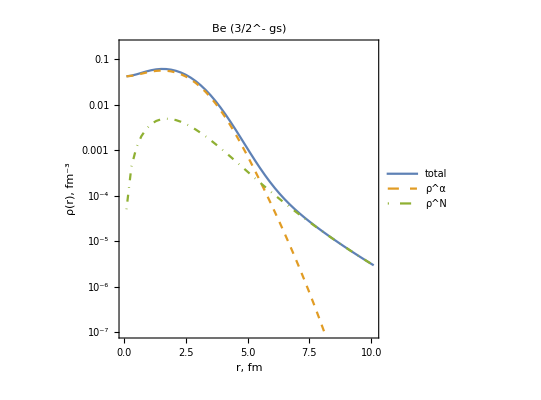

```mathematica
plotLabel=Piecewise[
{{"^6He (0^+ gs)",nucleus=="he"},{"^6Li (1^+ gs) ",nucleus=="li"},
{"Be (3/2^- gs)",nucleus=="be"}}];
rhoPlot=ListLogPlot[{totalData,αData,nData},
AspectRatio->1,
Frame->True,
Joined->True,
PlotLabel->plotLabel,
PlotRange->{Automatic,{10^-7,0.2}},
PlotLegends->{"total","ρ^α","ρ^N"},
PlotStyle->{Automatic,Dashed,DotDashed},
FrameLabel->{"r, fm","ρ(r), fm^-3"},
LabelStyle->Directive[Black,12],
FrameTicksStyle->Directive[Black,12],
FrameStyle->Directive[Black]]
```

```mathematica
Export[StringJoin[fileName,"_theDD",".pdf"],rhoPlot,"PDF"]
```

be/be0_theDD.pdf

## Comparison with the LLSM calculations for Hellium-6

### import data

```mathematica
"0.100000	0.109668
0.150000	0.108877
0.200000	0.108086
0.250000	0.106797
0.300000	0.105508
0.350000	0.103759
0.400000	0.102011
0.450000	0.099854
0.500000	0.097697
0.550000	0.095192
0.600000	0.092686
0.650000	0.089898
0.700000	0.087110
0.750000	0.084109
0.800000	0.081108
0.850000	0.077963
0.900000	0.074818
0.950000	0.071598
1.000000	0.068378
1.050000	0.065147
1.100000	0.061916
1.150000	0.058731
1.200000	0.055547
1.250000	0.052460
1.300000	0.049374
1.350000	0.046428
1.400000	0.043483
1.450000	0.040712
1.500000	0.037942
1.550000	0.035373
1.600000	0.032805
1.650000	0.030455
1.700000	0.028105
1.750000	0.025983
1.800000	0.023862
1.850000	0.021972
1.900000	0.020081
1.950000	0.018418
2.000000	0.016755
2.050000	0.015309
2.100000	0.013863
2.150000	0.012622
2.200000	0.011381
2.250000	0.010327
2.300000	0.009273
2.350000	0.008388
2.400000	0.007503
2.450000	0.006768
2.500000	0.006033
2.550000	0.005428
2.600000	0.004823
2.650000	0.004329
2.700000	0.003836
2.750000	0.003437
2.800000	0.003038
2.850000	0.002718
2.900000	0.002398
2.950000	0.002143
3.000000	0.001888
3.050000	0.001685
3.100000	0.001483
3.150000	0.001324
3.200000	0.001164
3.250000	0.001039
3.300000	0.000913
3.350000	0.000815
3.400000	0.000717
3.450000	0.000641
3.500000	0.000564
3.550000	0.000504
3.600000	0.000445
3.650000	0.000398
3.700000	0.000351
3.750000	0.000315
3.800000	0.000279
3.850000	0.000251
3.900000	0.000222
3.950000	0.000200
4.000000	0.000178
4.050000	0.000161
4.100000	0.000144
4.150000	0.000130
4.200000	0.000117
4.250000	0.000106
4.300000	0.000096
4.350000	0.000087
4.400000	0.000079
4.450000	0.000072
4.500000	0.000066
4.550000	0.000060
4.600000	0.000055
4.650000	0.000051
4.700000	0.000046
4.750000	0.000043
4.800000	0.000039
4.850000	0.000037
4.900000	0.000034
4.950000	0.000032
5.000000	0.000029
5.050000	0.000027
5.100000	0.000026
5.150000	0.000024
5.200000	0.000022
5.250000	0.000021
5.300000	0.000020
5.350000	0.000019
5.400000	0.000018
5.450000	0.000017
5.500000	0.000016
5.550000	0.000015
5.600000	0.000014
5.650000	0.000013
5.700000	0.000013
5.750000	0.000012
5.800000	0.000011
5.850000	0.000011
5.900000	0.000010
5.950000	0.000010
6.000000	0.000009
6.050000	0.000009
6.100000	0.000009
6.150000	0.000008
6.200000	0.000008
6.250000	0.000008
6.300000	0.000007
6.350000	0.000007
6.400000	0.000007
6.450000	0.000006
6.500000	0.000006
6.550000	0.000006
6.600000	0.000006
6.650000	0.000005
6.700000	0.000005
6.750000	0.000005
6.800000	0.000005
6.850000	0.000005
6.900000	0.000004
6.950000	0.000004
7.000000	0.000004
7.050000	0.000004
7.100000	0.000004
7.150000	0.000004
7.200000	0.000004
7.250000	0.000003
7.300000	0.000003
7.350000	0.000003
7.400000	0.000003
7.450000	0.000003
7.500000	0.000003
7.550000	0.000003
7.600000	0.000003
7.650000	0.000003
7.700000	0.000002
7.750000	0.000002
7.800000	0.000002
7.850000	0.000002
7.900000	0.000002
7.950000	0.000002
8.000000	0.000002
8.050000	0.000002
8.100000	0.000002
8.150000	0.000002
8.200000	0.000002
8.250000	0.000002
8.300000	0.000002
8.350000	0.000002
8.400000	0.000002
8.450000	0.000001
8.500000	0.000001
8.550000	0.000001
8.600000	0.000001
8.650000	0.000001
8.700000	0.000001
8.750000	0.000001
8.800000	0.000001
8.850000	0.000001
8.900000	0.000001
8.950000	0.000001
9.000000	0.000001
9.050000	0.000001
9.100000	0.000001
9.150000	0.000001
9.200000	0.000001
9.250000	0.000001
9.300000	0.000001
9.350000	0.000001
9.400000	0.000001
9.450000	0.000001
9.500000	0.000001
9.550000	0.000001
9.600000	0.000001
9.650000	0.000001
9.700000	0.000001
9.750000	0.000001
9.800000	0.000001
9.850000	0.000001
9.900000	0.000001
9.950000	0.000001
10.000000	0.000001
10.050000	0.000001
10.100000	0.000001
10.150000	0.000001";
protonLLSM=ImportString[%,"Table"];
"0.100000	0.111787
0.150000	0.111177
0.200000	0.110567
0.250000	0.109567
0.300000	0.108567
0.350000	0.107198
0.400000	0.105830
0.450000	0.104122
0.500000	0.102414
0.550000	0.100403
0.600000	0.098392
0.650000	0.096121
0.700000	0.093849
0.750000	0.091364
0.800000	0.088879
0.850000	0.086232
0.900000	0.083584
0.950000	0.080827
1.000000	0.078069
1.050000	0.075252
1.100000	0.072436
1.150000	0.069610
1.200000	0.066783
1.250000	0.063991
1.300000	0.061199
1.350000	0.058481
1.400000	0.055762
1.450000	0.053149
1.500000	0.050537
1.550000	0.048055
1.600000	0.045573
1.650000	0.043241
1.700000	0.040908
1.750000	0.038738
1.800000	0.036567
1.850000	0.034565
1.900000	0.032563
1.950000	0.030730
2.000000	0.028897
2.050000	0.027231
2.100000	0.025565
2.150000	0.024061
2.200000	0.022556
2.250000	0.021204
2.300000	0.019853
2.350000	0.018644
2.400000	0.017436
2.450000	0.016360
2.500000	0.015285
2.550000	0.014331
2.600000	0.013377
2.650000	0.012535
2.700000	0.011692
2.750000	0.010950
2.800000	0.010208
2.850000	0.009556
2.900000	0.008905
2.950000	0.008334
3.000000	0.007764
3.050000	0.007265
3.100000	0.006767
3.150000	0.006332
3.200000	0.005897
3.250000	0.005519
3.300000	0.005141
3.350000	0.004812
3.400000	0.004483
3.450000	0.004198
3.500000	0.003913
3.550000	0.003665
3.600000	0.003418
3.650000	0.003203
3.700000	0.002988
3.750000	0.002802
3.800000	0.002616
3.850000	0.002454
3.900000	0.002293
3.950000	0.002153
4.000000	0.002012
4.050000	0.001891
4.100000	0.001769
4.150000	0.001663
4.200000	0.001557
4.250000	0.001465
4.300000	0.001373
4.350000	0.001293
4.400000	0.001212
4.450000	0.001142
4.500000	0.001072
4.550000	0.001011
4.600000	0.000949
4.650000	0.000896
4.700000	0.000842
4.750000	0.000795
4.800000	0.000748
4.850000	0.000707
4.900000	0.000665
4.950000	0.000629
5.000000	0.000593
5.050000	0.000561
5.100000	0.000529
5.150000	0.000500
5.200000	0.000472
5.250000	0.000447
5.300000	0.000422
5.350000	0.000400
5.400000	0.000378
5.450000	0.000359
5.500000	0.000339
5.550000	0.000322
5.600000	0.000304
5.650000	0.000289
5.700000	0.000273
5.750000	0.000260
5.800000	0.000246
5.850000	0.000234
5.900000	0.000222
5.950000	0.000211
6.000000	0.000200
6.050000	0.000190
6.100000	0.000180
6.150000	0.000171
6.200000	0.000163
6.250000	0.000155
6.300000	0.000147
6.350000	0.000140
6.400000	0.000133
6.450000	0.000127
6.500000	0.000121
6.550000	0.000115
6.600000	0.000109
6.650000	0.000104
6.700000	0.000099
6.750000	0.000095
6.800000	0.000090
6.850000	0.000086
6.900000	0.000082
6.950000	0.000078
7.000000	0.000074
7.050000	0.000071
7.100000	0.000068
7.150000	0.000065
7.200000	0.000062
7.250000	0.000059
7.300000	0.000056
7.350000	0.000054
7.400000	0.000051
7.450000	0.000049
7.500000	0.000047
7.550000	0.000045
7.600000	0.000043
7.650000	0.000041
7.700000	0.000039
7.750000	0.000037
7.800000	0.000036
7.850000	0.000034
7.900000	0.000033
7.950000	0.000031
8.000000	0.000030
8.050000	0.000029
8.100000	0.000027
8.150000	0.000026
8.200000	0.000025
8.250000	0.000024
8.300000	0.000023
8.350000	0.000022
8.400000	0.000021
8.450000	0.000020
8.500000	0.000019
8.550000	0.000019
8.600000	0.000018
8.650000	0.000017
8.700000	0.000016
8.750000	0.000016
8.800000	0.000015
8.850000	0.000015
8.900000	0.000014
8.950000	0.000013
9.000000	0.000013
9.050000	0.000012
9.100000	0.000012
9.150000	0.000011
9.200000	0.000011
9.250000	0.000010
9.300000	0.000010
9.350000	0.000010
9.400000	0.000009
9.450000	0.000009
9.500000	0.000009
9.550000	0.000008
9.600000	0.000008
9.650000	0.000008
9.700000	0.000007
9.750000	0.000007
9.800000	0.000007
9.850000	0.000007
9.900000	0.000006
9.950000	0.000006
10.000000	0.000006
10.050000	0.000005
10.100000	0.000005
10.150000	0.000005";
neutronLLSM=ImportString[%,"Table"];
```

### Plot results

```mathematica
If[nucleus=="he",

dataLLSM=Transpose[{neutronLLSM⟦All,1⟧,neutronLLSM⟦All,2⟧+protonLLSM⟦All,2⟧}];
compPlot=ListLogPlot[{totalData,dataLLSM},
AspectRatio->1,
Frame->True,
Joined->True,
PlotLegends->{"3BM","LLSM"},
PlotStyle->{Automatic,Dashed,DotDashed},
FrameLabel->{"r, fm","ρ(r), fm^-3"},
LabelStyle->Directive[Black,12],
FrameTicksStyle->Directive[Black,12],
FrameStyle->Directive[Black]];
Export[StringJoin[fileName,"_compPlot",".pdf"],compPlot,"PDF"];
compPlot
]
```

## Export Data

```mathematica
(*Export[StringJoin[fileName,"_theDD",".pdf"],graph1,"pdf"];*)
```

```mathematica
(*𝒩*)
```

```mathematica
(*{StringRiffle[γ⟦#⟧]}&/@Range[Length@γ]

*)
```

```mathematica
(*StringRiffle[γ⟦#⟧]&/@Range[Length@γ];
Transpose[{%,𝒩}];
StringJoin["<rms>^1/2_m = ",ToString[rms],"\n",StringRiffle[%]]
Export[StringJoin[fileName,".norm"],%,"Text"];*)
```

```mathematica
(*graph2=ContourPlot[Sum[x^(2+2γ⟦k,1⟧)y^(2+2γ⟦k,2⟧)Total[Cij⟦k⟧Exp[-1/2αij⟦k⟧x^2-1/2 βij⟦k⟧y^2]],{k,γForCalc}],{x,0.1,8},{y,0.1,8},PlotRange->Full,AspectRatio->1.,ImageSize->Small,FrameLabel->{"x","y"},PlotLabel->"x^2y^2|Ψ(x,y)|^2"]*)
```

```mathematica
(*Export[StringJoin[fileName,"_theCP",".jpg"],graph2,"jpg",ImageResolution->1000];*)
```

```mathematica
(*graph3=Plot3D[Sum[x^(2+2γ⟦k,1⟧)y^(2+2γ⟦k,2⟧)Total[Cij⟦k⟧Exp[-1/2αij⟦k⟧x^2-1/2 βij⟦k⟧y^2]],{k,γForCalc}],{x,0,8},{y,0,8},PlotRange->Full,AspectRatio->1.5,PerformanceGoal->"Quality",ImageSize->Small,AxesLabel->{"x, fm","y, fm"},PlotLabel->"x^2y^2|Ψ(x,y)|^2"]*)
```

```mathematica
(*Export[StringJoin[fileName,"_the3D",".jpg"],graph3,"jpg",ImageResolution->1000];*)
```

```mathematica
(*f77Eform[x_?NumericQ,fw_Integer,ndig_Integer]:=Module[{sig,s,p,ps},{s,p}=MantissaExponent[x];
{sig,ps}={ToString[Round[10^ndig Abs[s]]],ToString[Abs[p]]};
StringJoin@@Join[Table[" ",{fw-ndig-7}],If[x<0,"-"," "],{"0."},{sig},Table["0",{ndig-StringLength[sig]}],{"E"},If[p<0,{"-"},{"+"}],Table["0",{2-StringLength[ps]}],{ps}]];*)
```

```mathematica
(*
Do[
Print["\\midrule"];
rowString=StringJoin["\\multicolumn{4}{c}{ $\\gamma \\equiv $  ", StringRiffle[γ⟦k⟧],"} \\\\"];
Print[rowString];
Print["\\midrule"];
Do[
Print[StringJoin[ToString[i],"  &  ", ToString[NumberForm[2.dataList⟦k,i,1⟧,{8,8}]],"  &  ", ToString[NumberForm[2.dataList⟦k,i,2⟧,{8,8}]], "  &  ",  ToString[f77Eform[dataList⟦k,i,3⟧,10,10]] ," \\\\"]];
,{i,1,Length@dataList⟦k,All,3⟧}];
,{k,1,Length@dataList⟦All,1,3⟧}];*)
```

## Export density functions

```mathematica
(*Block[{r,rMin=0.01,rMax=10.01,rH=10.0/200.,tot, k,p},
r=Table[NumberForm[r,{4,4}],{r,rMin,rMax,rH}];
Print[r];
tot=Transpose@{r,Table[f77Eform[𝒩1 ρ1[r]+𝒩2 ρ2[r],6,6],{r,rMin,rMax,rH}]};
k=Transpose@{r,Table[f77Eform[𝒩1 ρ1[r],6,6],{r,rMin,rMax,rH}]};
p=Transpose@{r,Table[f77Eform[𝒩2 ρ2[r],6,6],{r,rMin,rMax,rH}]};
Export[StringJoin[fileName,"_tot.ddt"],tot,"Table"];
Export[StringJoin[fileName,"_k.ddt"],k,"Table"];
Export[StringJoin[fileName,"_p.ddt"],p,"Table"];
{rMax, rMin,rH}
]*)
```